```mathematica
electroStaticPotential[q_,p_,r_] :=Sum[ q[[i]]/Norm[r-p[[i]]], {i,Length[q]}]
```

```mathematica
electricField[{q1_,q2_},{{x1_,y1_,z1_},{x2_,y2_,z2_}}]=-D[electroStaticPotential[{q1,q2},{{x1,y1,z1},{x2,y2,z2}},{x,y,z}],{{x,y,z}}]/.Abs'[x_]:>x/(√(x^2));
```

```mathematica
v=VectorPlot3D[electricField[{1,-1},{{-1,0,0},{1,0,0}}],{x,-6,6},{y,0,4},{z,-4,4},VectorPoints->5]
```

-Graphics3D-

```mathematica
v=VectorPlot3D[electricField[{1,-1},{{-1,0,0},{1,0,0}}],{x,-6,6},{y,0,4},{z,-4,4},VectorPoints->5,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export[File[FileNameJoin[{NotebookDirectory[],"eletric potential 3D vector field.svg"}]],VectorPlot3D[electricField[{1,-1},{{-1,0,0},{1,0,0}}],{x,-6,6},{y,0,4},{z,-4,4},VectorPoints->5,ImageSize->Large]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\eletric potential 3D vector field.svg

```mathematica
RenameFile["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\eletric potential 3D vector field.svg",FileNameJoin[{NotebookDirectory[],"electric potential 3D vector field.svg"}]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\electric potential 3D vector field.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\electric potential 3D vector field.svg"]
```

## Image of Pi

```mathematica
image=ColorConvert[Rasterize[π,ImageSize->40,RasterSize->40],"Grayscale"]
```

-Graphics-

```mathematica
{dx,dy}=Table[ImageAdjust@GaussianFilter[image,{6,2}, δ],{δ,{{1,0},{0,1}}}]
```

{-Graphics-,-Graphics-}

```mathematica
data=Reverse/@Transpose[2ImageData/@{dx,dy}-1,{3,2,1}];
```

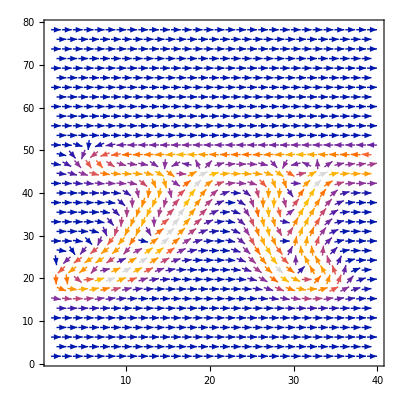

```mathematica
ListVectorPlot[data,VectorPoints->30]
```

```mathematica
ListVectorPlot[data,VectorPoints->30,ImageSize->Full]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"vector field of rasterized pi with gaussian derivatives.svg"}],ListVectorPlot[data,VectorPoints->30,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\vector field of rasterized pi with gaussian derivatives.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\vector field of rasterized pi with gaussian derivatives.svg"]
```

```mathematica
Reverse/@Transpose[2ImageData/@Table[ImageAdjust@GaussianFilter[ColorConvert[Rasterize[π,ImageSize->40,RasterSize->40],"Grayscale"],{6,2}, δ],{δ,{{1,0},{0,1}}}]-1,{3,2,1}]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"vector field of rasterized base of the natural logarithm e with gaussian derivatives.svg"}],ListVectorPlot[Reverse/@Transpose[2ImageData/@Table[ImageAdjust@GaussianFilter[ColorConvert[Rasterize[ⅇ,ImageSize->40,RasterSize->40],"Grayscale"],{6,2}, δ],{δ,{{1,0},{0,1}}}]-1,{3,2,1}],VectorPoints->30,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\vector field of rasterized base of the natural logarithm e with gaussian derivatives.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\vector field of rasterized base of the natural logarithm e with gaussian derivatives.svg"]
```

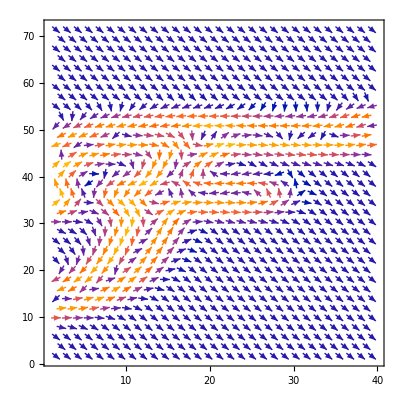

```mathematica
ListVectorPlot[Reverse/@Transpose[2ImageData/@Table[ImageAdjust@GaussianFilter[ColorConvert[Rasterize[ℱ,ImageSize->40,RasterSize->40],"Grayscale"],{6,2}, δ],{δ,{{1,0},{0,1}}}]-1,{3,2,1}],VectorPoints->30,ImageSize->Full]
```

```mathematica
ResourceFunction["ResourceSubmissions"][]
```

{ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…],ResourceSubmissionObject[…]}